## Вычеты и их применение.

### Теоремы о вычетах и их применение к вычислению конурных интегралов.

№12.434 Используя теоремы о вычетах, вычислить следующий интеграл:

∫_(C^+) z/((z-1)(z-2))ⅆz,  C={z | |z-2|=2}

Для этого воспользуемся Первой теоремой о вычетах:

∫_(С^+) f(z)ⅆz=2πⅈ∑_(k=1)^N res(f(z);z_k)

Найдем все полюса функции f(z)

```mathematica
f[z_]:=z/((z-1)(z-2))
```

Конечно видно, что полюсами будут точки z_1=1 и z_2=2, но всё же применим более общий способ:

```mathematica
sol=Solve[f[z]^-1==0,z]
```

{{z→1},{z→2}}

Теперь нужно определить, какие из найденных полюсов охватываются контуром С.

1) Определим графически.

Для этого изобразим контур С, и найденые нами полюса.

```mathematica
Show[ ContourPlot[(x-2)^2+y^2==4,{x,0,4},{y,-2,2},AxesLabel->{Re,Im},PlotRange->{{-1,5},{-3,3}} ,Frame->False,Axes->True],Graphics[{PointSize[Large],Red,Point[ReIm[z/.sol]]} ] ]
```

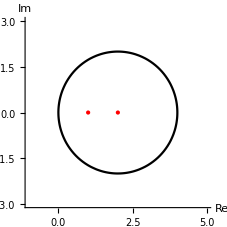

Из рисунка видно, что обе точки лежат внутри контура С.

Найдем интеграл по первой теореме вычетов (1).

```mathematica
int=2π ⅈ Sum[Residue[f[z],{z,z/.sol[[i]]}],{i,1,Length[sol]}]
```

2 ⅈ π

2) Определим аналитически.

Будем брать каждый i-ый полюс,проверять растояние от него до точки (2,0) - центра окружности, и если оно меньше заданного радиуса, будем считать в нем вычет.

```mathematica
int1=2π ⅈ Sum [ If[ Abs[ -2+z/.sol[[i]]]≤ 2,Residue[f[z],{z,z/.sol[[i]] } ],0],{i,1,Length[z/.sol]} ]
```

2 ⅈ π

Получился тотже самый, правильный ответ.

Итак, это общий алгоритм решения такого класса задач, в которых НЕТ существенно особых точек, используя который можно, заменяя вверху функцию f[z_] на одну из тех, которые есть в задачах №№ 12.435, ........ , получить ответы их решения (см. таблицу ответов). Читатель же теперь может найти эти решения и ответы самостоятельно.

Итак конечный ответ:

∫_(C^+) z/((z-1)(z-2))ⅆz=2 ⅈ π